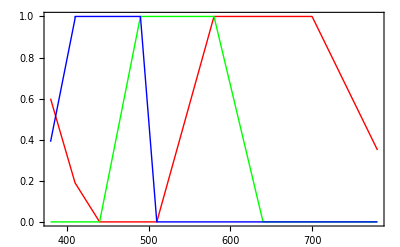

```mathematica
Plot[{toRGB[wavelength][[1]],toRGB[wavelength][[2]],toRGB[wavelength][[3]]},{wavelength,380,780},PlotStyle->{Red,Green,Blue},Frame->True]
```

```mathematica
Clear[wavelength]
```

```mathematica
toRGB[wavelength_]:=Piecewise[{{{0.6 - 0.41(wavelength-380)/30,0,0.39 + 0.6(wavelength-380)/30},wavelength ≥ 380.0 && wavelength ≤ 410.0},{{0.19 - 0.19(wavelength-410)/30,0,1},wavelength ≥ 410.0 && wavelength ≤ 440.0},{{0,1 - (490-wavelength)/50,1},wavelength ≥ 440.0 && wavelength ≤ 490.0},{{0,1,(510-wavelength)/20},wavelength ≥ 490.0 && wavelength ≤ 510.0},{{1 - (580-wavelength)/70,1,0},wavelength ≥ 510.0 && wavelength ≤ 580.0},
{{1,(640-wavelength)/60,0},wavelength ≥ 580.0 && wavelength ≤ 640.0},
{{1,0,0},wavelength ≥ 640.0 && wavelength ≤ 700.0},
{{0.35 + 0.65(780-wavelength)/80,0,0},wavelength ≥ 700.0 && wavelength ≤ 780.0}}]
```

```mathematica
toRGB[wavelength_]:=Piecewise[{{{0.6 - 0.41(410-wavelength)/30,0,0.39 + 0.6(410-wavelength)/30},wavelength ≥ 380.0 && wavelength ≤ 410.0},{{0.19 - 0.19(440-wavelength)/30,0,1},wavelength ≥ 410.0 && wavelength ≤ 440.0},{{0,1 - (490-wavelength)/50,1},wavelength ≥ 440.0 && wavelength ≤ 490.0},{{0,1,(510-wavelength)/20},wavelength ≥ 490.0 && wavelength ≤ 510.0},{{1 - (580-wavelength)/70,1,0},wavelength ≥ 510.0 && wavelength ≤ 580.0},
{{1,(640-wavelength)/60,0},wavelength ≥ 580.0 && wavelength ≤ 640.0},
{{1,0,0},wavelength ≥ 640.0 && wavelength ≤ 700.0},
{{0.35 + 0.65(780-wavelength)/80,0,0},wavelength ≥ 700.0 && wavelength ≤ 780.0}}]
```

```mathematica
toRGB[λ]
```

Piecewise[{{{0.6-0.0136667 (-380+λ),0,0.39+0.02 (-380+λ)}, λ≥380.&&λ≤410.}, {{0.19-0.00633333 (-410+λ),0,1}, λ≥410.&&λ≤440.}, {{0,1+1/50 (-490+λ),1}, λ≥440.&&λ≤490.}, {{0,1,(510-λ)/20}, λ≥490.&&λ≤510.}, {{1+1/70 (-580+λ),1,0}, λ≥510.&&λ≤580.}, {{1,(640-λ)/60,0}, λ≥580.&&λ≤640.}, {{1,0,0}, λ≥640.&&λ≤700.}, {{0.35+0.008125 (780-λ),0,0}, λ≥700.&&λ≤780.}, {0, True}}]

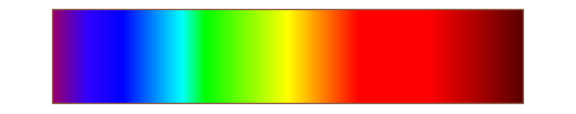

```mathematica
ParametricPlot[{x,y},{x,380,780},{y,0,1},
ColorFunction->(RGBColor@@toRGB[#1]&),
ColorFunctionScaling->False, (* Do *not* scale #1 to 0..1! *)
BaseStyle->{FontSize->14},
AxesOrigin->{400,0},
Axes->None,
Ticks->None,
Frame->False,
Mesh->None,ImagePadding->All,
AspectRatio->.2,
PlotPoints->{1024,2},
ImageSize->Large
]
```

```mathematica
OxyHemoglobin={415,540,570};
DeoxyHemoglobin={430,555};
```

{415,540,570}

{430,555}

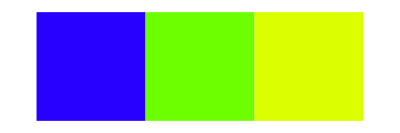

```mathematica
Graphics[{RGBColor[0.1583,0,1],Rectangle[{0,0},{1,1}],RGBColor[3/7,1,0],Rectangle[{1,0},{2,1}],RGBColor[6/7,1,0],Rectangle[{2,0},{3,1}]}]
```

```mathematica
Graphics[{RGBColor[Transpose[OxyHemoglobinRGB][[1]]],Rectangle[{0,0},{1,1}],RGBColor[Transpose[OxyHemoglobinRGB][[2]]],Rectangle[{1,0},{2,1}],RGBColor[Transpose[OxyHemoglobinRGB][[3]]],Rectangle[{2,0},{3,1}]}]
```

-Graphics-

```mathematica
OxyHemoglobinRGB = Transpose[Map[toRGB,OxyHemoglobin]]
DeoxyHemoglobinRGB = Transpose[Map[toRGB,DeoxyHemoglobin]]
```

{{0.158333,3/7,6/7},{0,1,1},{1,0,0}}

{{0.0633333,9/14},{0,1},{1,0}}

```mathematica
nYAB[-0.1537].OxyHemoglobinRGB + {{0,0,0},{0.5,0.5,0.5},{0.5,0.5,0.5}}
```

{{0.193056,0.238095,0.309524},{0.846045,0.0783929,0.156786},{0.161267,0.632185,0.846471}}

```mathematica
AppendTo[$Path, NotebookDirectory[]]
```

```mathematica
AbsOxyHemo = Import["AbsorbanceOxyHemo.csv"];
AbsDeOxyHemo = Import["AbsorbanceDeOxyHemo.csv"];
AbsMel= Import["AbsorbanceMel.csv"];
```

```mathematica
blueEye= Import["EyeRGB_Blue_Gaussian.csv"];
greenEye= Import["EyeRGB_Green_Gaussian.csv"];
redEye= Import["EyeRGB_Red_Gaussian.csv"];
```

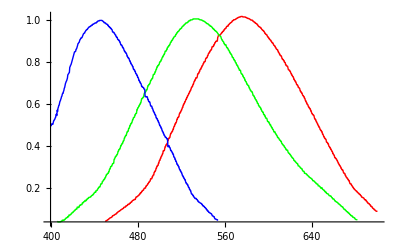

```mathematica
Grid[{{ListLinePlot[{redEye,greenEye,blueEye},PlotRange->All, PlotStyle->{Red,Green,Blue}]}}]
```

```mathematica
σRGB={60,60,60}; μRGB ={580,530,450};
```

```mathematica
gaussian[λ_,μ_,σ_]:= Exp[-(λ-μ)^2/(2*σ^2)];
{σRGB[[1]],μRGB[[1]]}={σ,μ}/.FindFit[redEye,gaussian[λ,μ,σ],{{σ,σRGB[[1]]},{ μ, μRGB[[1]]}},λ]
{σRGB[[2]],μRGB[[2]]}={σ,μ}/.FindFit[greenEye,gaussian[λ,μ,σ],{{σ,σRGB[[2]]},{ μ, μRGB[[2]]}},λ]
{σRGB[[3]],μRGB[[3]]}={σ,μ}/.FindFit[blueEye,gaussian[λ,μ,σ],{{σ,σRGB[[3]]},{ μ, μRGB[[3]]}},λ]
```

{54.7737,579.468}

{55.2905,537.948}

{42.7746,448.143}

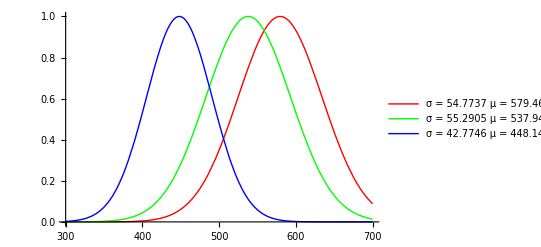

```mathematica
Plot[{gaussian[λ,μRGB[[1]] ,σRGB[[1]]],gaussian[λ,μRGB[[2]],σRGB[[2]]],gaussian[λ,μRGB[[3]],σRGB[[3]]]},{λ,300,700},PlotRange->All, PlotStyle->{Red,Green,Blue},PlotLegends->{StringJoin[{"σ = ",ToString[σRGB[[1]]],"  μ = ",ToString[μRGB[[1]]]}],StringJoin[{"σ = ",ToString[σRGB[[2]]],"  μ = ",ToString[μRGB[[2]]]}],StringJoin[{"σ = ",ToString[σRGB[[3]]],"  μ = ",ToString[μRGB[[3]]]}]}]
```

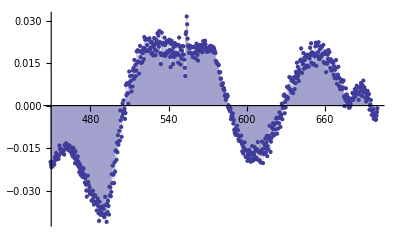

```mathematica
residuals=redEye[[All,2]]-Map[gaussian[#1,μRGB[[1]],σRGB[[1]]]&,redEye[[All,1]]];
ListPlot[residuals,Filling->Axis,DataRange->{Min[redEye[[All,1]]],Max[redEye[[All,1]]]},PlotRange->{All,All}]
```

```mathematica
ScatOxyHemo = AbsOxyHemo;
ScatOxyHemo[[All,2]] = 1- AbsOxyHemo[[All,2]];
ScatDeOxyHemo = AbsDeOxyHemo;
ScatDeOxyHemo[[All,2]] = 1- AbsDeOxyHemo[[All,2]];
ScatMel = AbsMel;
ScatMel[[All,2]] = 1- AbsMel[[All,2]];
```

```mathematica
eScatOxyHemo = AbsOxyHemo;
eScatOxyHemo[[All,2]] =10^(-AbsOxyHemo[[All,2]]);
eScatDeOxyHemo = AbsDeOxyHemo;
eScatDeOxyHemo[[All,2]] = 10^(-AbsDeOxyHemo[[All,2]]);
eScatMel = AbsMel;
eScatMel[[All,2]] = 10^(-AbsMel[[All,2]]);
```

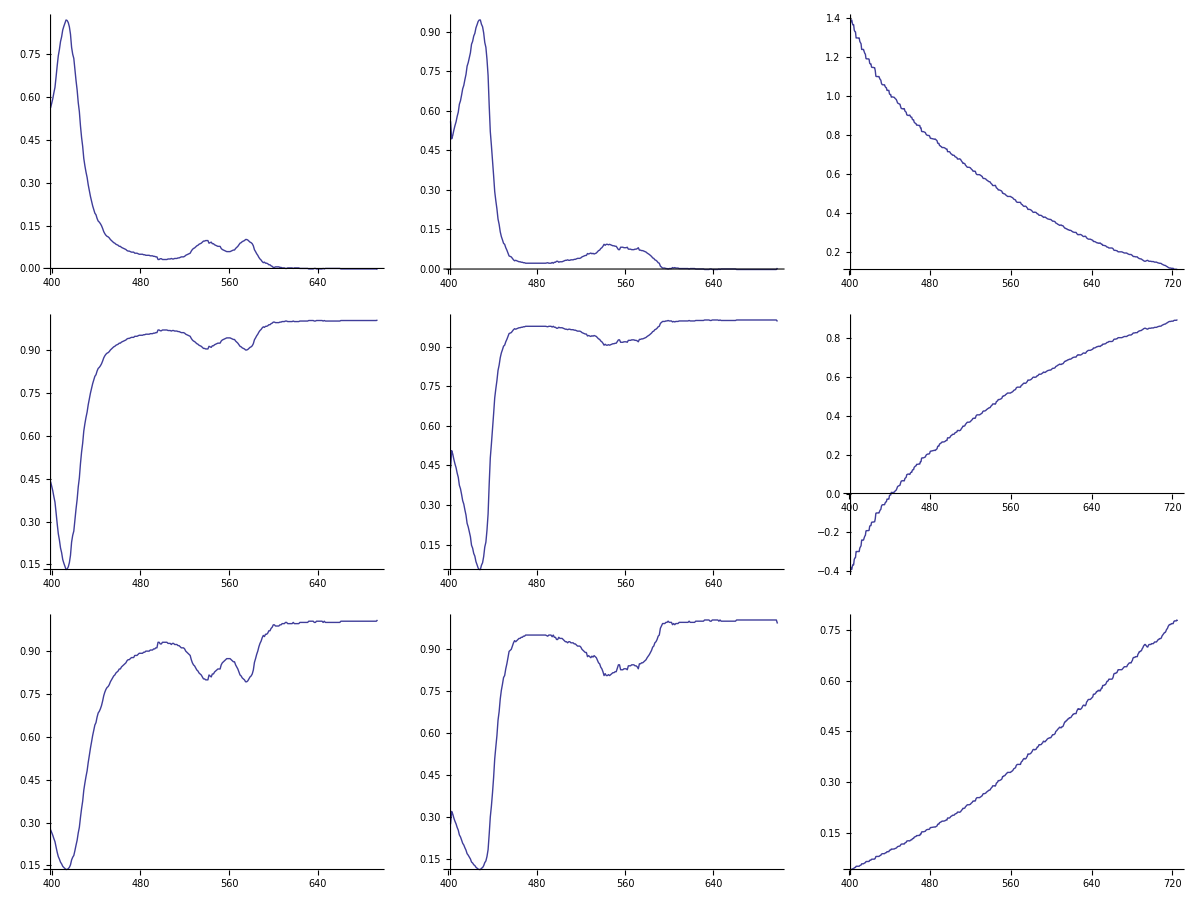

```mathematica
Grid[{{ListLinePlot[AbsOxyHemo,PlotRange->All],ListLinePlot[AbsDeOxyHemo,PlotRange->All],ListLinePlot[AbsMel,PlotRange->All]},
{ListLinePlot[ScatOxyHemo,PlotRange->All],ListLinePlot[ScatDeOxyHemo,PlotRange->All],ListLinePlot[ScatMel,PlotRange->All]},
{ListLinePlot[eScatOxyHemo,PlotRange->All],ListLinePlot[eScatDeOxyHemo,PlotRange->All],ListLinePlot[eScatMel,PlotRange->All]}}]
```

```mathematica
FindFit[eScatOxyHemo,{r gaussian[λ,μRGB[[1]] ,σRGB[[1]]]+g gaussian[λ,μRGB[[2]],σRGB[[2]]]+b gaussian[λ,μRGB[[3]],σRGB[[3]]],{r>0,g>0,b>0}},{r,g,b},λ]
```

{r→1.17313,g→2.96298×10^-7,b→0.637874}

```mathematica
RGBModel[λ_,rgb_]:=rgb[[1]] gaussian[λ,μRGB[[1]] ,σRGB[[1]]]+rgb[[2]] gaussian[λ,μRGB[[2]],σRGB[[2]]]+rgb[[3]] gaussian[λ,μRGB[[3]],σRGB[[3]]];
RGBValues[data_]:=Module[{},
rgbTotals = {r,g,b}/.FindFit[data,{RGBModel[λ,{r,g,b}],{0<r<1,0<g<1,0<b<1}},{{r,0.5},{g,0.5},{b,0.5}},λ];
rgbTotals/Max[rgbTotals]]
```

```mathematica
RGBValues[eScatOxyHemo]
RGBValues[eScatDeOxyHemo]
RGBValues[eScatMel]
```

{1.,0.125392,0.607639}

{1.,0.160659,0.547293}

{1.,1.06159×10^-7,0.11393}

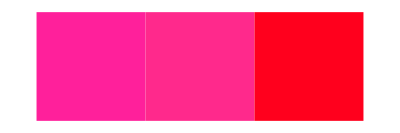

```mathematica
Graphics[{RGBColor[RGBValues[eScatOxyHemo]],Rectangle[{0,0},{1,1}],RGBColor[RGBValues[eScatDeOxyHemo]],Rectangle[{1,0},{2,1}],RGBColor[RGBValues[eScatMel]],Rectangle[{2,0},{3,1}]}]
```

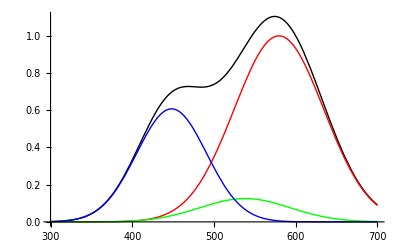

```mathematica
rgb=RGBValues[eScatOxyHemo];Plot[{RGBModel[λ,rgb],rgb[[1]] gaussian[λ,μRGB[[1]] ,σRGB[[1]]],rgb[[2]] gaussian[λ,μRGB[[2]],σRGB[[2]]],rgb[[3]] gaussian[λ,μRGB[[3]],σRGB[[3]]] },{λ,300,700},PlotRange->All, PlotStyle->{Black,Red,Green,Blue}]
```

```mathematica
Plot[r gaussian[λ,μRGB[[1]] ,σRGB[[1]]]+g gaussian[λ,μRGB[[2]],σRGB[[2]]]+b gaussian[λ,μRGB[[3]],σRGB[[3]]]
```

```mathematica
RGBGaussian[data_,idx_]:=Map[{#1[[1]], gaussian[#1[[1]],μRGB[[idx]] ,σRGB[[idx]]] #1[[2]]}&,data]
```

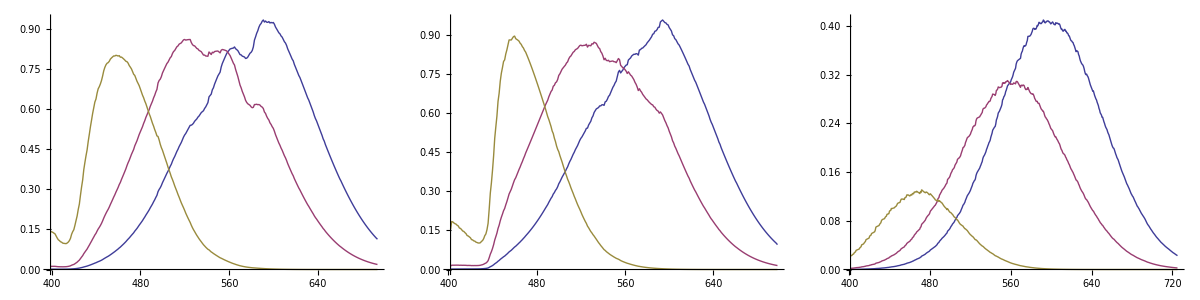

```mathematica
Grid[{{ListLinePlot[{RGBGaussian[eScatOxyHemo,1],RGBGaussian[eScatOxyHemo,2],RGBGaussian[eScatOxyHemo,3]},PlotRange->All],ListLinePlot[{RGBGaussian[eScatDeOxyHemo,1],RGBGaussian[eScatDeOxyHemo,2],RGBGaussian[eScatDeOxyHemo,3]},PlotRange->All],ListLinePlot[{RGBGaussian[eScatMel,1],RGBGaussian[eScatMel,2],RGBGaussian[eScatMel,3]},PlotRange->All]}}]
```

```mathematica
eScatOxyHemo[[-1,1]]
```

694

```mathematica
RGBValues[data_]:=Module[{},rgbTotals = {Integrate[Interpolation[RGBGaussian[data,1],InterpolationOrder->1][x],{x,data[[1,1]],data[[-1,1]]}],Integrate[Interpolation[RGBGaussian[data,2],InterpolationOrder->1][x],{x,data[[1,1]],data[[-1,1]]}],Integrate[Interpolation[RGBGaussian[data,3],InterpolationOrder->1][x],{x,data[[1,1]],data[[-1,1]]}]};
rgbTotals/Max[rgbTotals]]
```

```mathematica
RGBValues[eScatOxyHemo]
RGBValues[eScatDeOxyHemo]
RGBValues[eScatMel]
```

{1.,0.972115,0.509046}

{1.,0.970484,0.480847}

{1.,0.756442,0.225578}

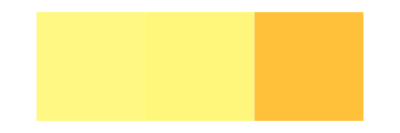

```mathematica
Graphics[{RGBColor[RGBValues[eScatOxyHemo]],Rectangle[{0,0},{1,1}],RGBColor[RGBValues[eScatDeOxyHemo]],Rectangle[{1,0},{2,1}],RGBColor[RGBValues[eScatMel]],Rectangle[{2,0},{3,1}]}]
```